```mathematica
Options[legendMaker]=Join[FilterRules[Options[Framed],Except[{ImageSize,FrameStyle,Background,RoundingRadius,ImageMargins}]],{FrameStyle->None,Background->Directive[Opacity[.7],LightGray],RoundingRadius->10,ImageMargins->0,PlotStyle->Automatic,PlotMarkers->None,"LegendLineWidth"->35,"LegendLineAspectRatio"->.3,"LegendMarkerSize"->8,"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}}];

legendMaker[textLabels_,opts:OptionsPattern[]]:=Module[{f,lineDirectives,markerSymbols,n=Length[textLabels],x},lineDirectives=((PlotStyle/.{opts})/.PlotStyle|Automatic:>Map[ColorData[1],Range[n]])/.None->{None};
markerSymbols=Replace[((PlotMarkers/.{opts})/.Automatic:>(Drop[ListPlot[Transpose[{Range[n]}],PlotMarkers->Automatic][[1,2]][[1]],-1]/.Inset[x_,i__]:>x)[[All,-1]])/.{Graphics[gr__],sc_}:>Graphics[gr,ImageSize->("LegendMarkerSize"/.{opts}/.Options[legendMaker,"LegendMarkerSize"]/.{"LegendMarkerSize"->8})],PlotMarkers|None:>Map[Style["",Opacity[0]]&,textLabels]]/.None|{}->Style["",Opacity[0]];
lineDirectives=PadRight[lineDirectives,n,lineDirectives];
markerSymbols=PadRight[markerSymbols,n,markerSymbols];
f=Grid[MapThread[{Graphics[{#1/.None->{},If[#1==={None}||(PlotStyle/.{opts})===None,{},Line[{{-.1,0},{.1,0}}]],Inset[#2,{0,0},Background->None]},AspectRatio->("LegendLineAspectRatio"/.{opts}/.Options[legendMaker,"LegendLineAspectRatio"]/.{"LegendLineAspectRatio"->.2}),ImageSize->("LegendLineWidth"/.{opts}/.Options[legendMaker,"LegendLineWidth"]/.{"LegendLineWidth"->35}),ImagePadding->{{1,1},{0,0}}],Text[#3,FormatType->TraditionalForm]}&,{lineDirectives,markerSymbols,textLabels}],Sequence@Evaluate[("LegendGridOptions"/.{opts}/.Options[legendMaker,"LegendGridOptions"]/.{"LegendGridOptions"->{Alignment->Left,Spacings->{.4,.1}}})]];
Framed[f,FilterRules[{Sequence[opts,Options[legendMaker]]},FilterRules[Options[Framed],Except[ImageSize]]]]];


extractStyles[plot_]:=Module[{lines,markers,extract=First[Normal[plot]]},(*In a plot,the list of lines contains no insets,so I use this to find it:*)lines=Select[extract,FreeQ[#1,Inset]&];
(*Most plot markers are inside Inset,except for Point in list plots:*)markers=Select[extract,!FreeQ[#1,Inset]&];
(*The function returns a list of lists:*){(*The first return value is the list of line plot styles:*)Replace[Cases[lines,{c__,Line[__],___}:>Flatten[Directive@@Cases[{c},Except[_Line]]],Infinity],{}->None],(*Second return value:marker symbols*)Replace[Join[Cases[markers,{c__,Inset[s_,pos_,d___],e___}:>If[(*markers "s" can be strings or graphics*)Head[s]===Graphics,(*Append scale factor in case it's needed later;
default 0.01*){s,Last[{.01,d}]/.Scaled[f_]:>First[f]},If[(*For strings,add line color if no color specified via text styles:*)FreeQ[s,CMYKColor|RGBColor|GrayLevel|Hue],Style[s,c],s]],Infinity],(*"Point" counts as marker but appears in "lines".Filter out Pointsize-legends don't need it:*)Cases[lines,{c___,PointSize[_],d___,Point[pt__],___}:>{Graphics[{c,d,Point[{0,0}]}],.01},Infinity]],{}->None]}]

Options[autoLegend]={Alignment->{Right,Top},Background->White,AspectRatio->Automatic};
autoLegend[plot_Graphics,labels_,opts:OptionsPattern[]]:=Module[{lines,markers,align=OptionValue[Alignment]},{lines,markers}=extractStyles[plot];
Graphics[{Inset[plot,{-1,-1},{Left,Bottom},Scaled[1]],Inset[legendMaker[labels,PlotStyle->lines,PlotMarkers->markers,opts],align,Map[If[NumericQ[#],Center,#]&,align]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->(OptionValue[AspectRatio]/.Automatic:>(AspectRatio/.Options[plot,AspectRatio])/.Automatic:>(AspectRatio/.AbsoluteOptions[plot,AspectRatio]))]]
```

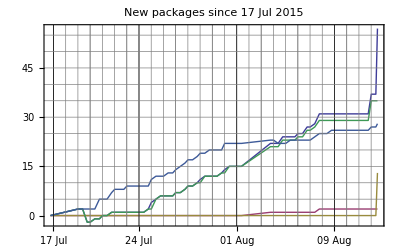
-Graphics--Graphics- | Total
-Graphics- | Gnu
-Graphics- | Marmalade
-Graphics- | Melpa
-Graphics- | Melpa Stable

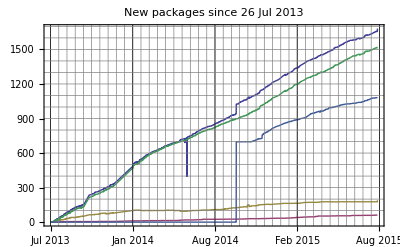
-Graphics--Graphics- | Total
-Graphics- | Gnu
-Graphics- | Marmalade
-Graphics- | Melpa
-Graphics- | Melpa Stable

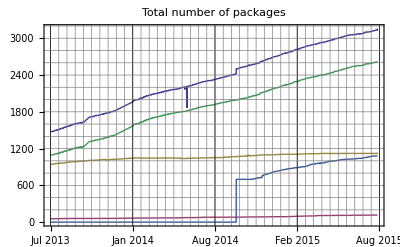
-Graphics--Graphics- | Total
-Graphics- | Gnu
-Graphics- | Marmalade
-Graphics- | Melpa
-Graphics- | Melpa Stable

```mathematica
(*NotebookEvaluate[StringJoin[Directory[], "/legendMaker.nb"]]; *)
dataDir1 = StringJoin[Directory[],  "/"]; 
leg = {"Total", "Gnu", "Marmalade", "Melpa", "Melpa Stable"}; 

importWithDate[n_Integer] := ({DateList[{#1[[1]], {"Year", "-", "Month", "-", "Day", "T", "Hour", ":", "Minute"}}], #1[[2]]} & ) /@ 
    Import[StringJoin[dataDir1, "main-dish.dat"], {"Data", "All", {2, n}}]; 
totalCount = importWithDate[3]; 
singleCount = importWithDate[4]; 
tarCount = importWithDate[5]; 
gnuCount = importWithDate[6]; 
marmaladeCount = importWithDate[7]; 
melpaCount = importWithDate[8]; 
stableCount = importWithDate[9]; 
today = Take[DateList[], 3]; 
takeAfterDate=Function[{list,date},Drop[list, (Position[#1, First[Nearest[#1, AbsoluteTime[date]]]] & )[AbsoluteTime /@ list[[All,1]]][[1,1]] - 1]];
countToGrowth=Function[{list,date}, Module[{iv = takeAfterDate[list,date]},({#1[[1]], #1[[2]] - iv[[1,2]]} & ) /@ iv]]; 
bigPlot[rs_, re_,dateFormat_,filterFunction_,label_,tickStep_] := (Overlay[{#1, legendMaker[leg]}, Alignment -> {-0.7, 0.7}] & )[
    DateListPlot[(filterFunction[#1, rs] & ) /@ {totalCount, gnuCount, marmaladeCount, melpaCount,stableCount},
PlotLabel->If[label,label,StringJoin["New packages since ", DateString[rs, {"Day", " ", "MonthNameShort", " ", "Year"}]],label],
Joined -> True,
AxesStyle -> Directive[Thickness[0.004]], 
DateTicksFormat -> dateFormat,
GridLines -> {Join[({#1, Gray} & ) /@ DateRange[rs, re, Quantity[DateDifference[rs, re]/40, "Day"]],
({#1, Black} & ) /@ DateRange[rs, re, Quantity[DateDifference[rs, re]/4, "Day"]]],
({#1, Gray} & ) /@ Array[tickStep*#1 & , 200]},
FrameTicks -> {Automatic, {DateRange[rs, re, Quantity[DateDifference[rs, re]/4, "Day"]], None}}, Method -> {"AxesInFront" -> False}]]; 
rangeStart = DatePlus[today, {{-1, "Month"}}]; 
(* Do the plots *)
newPackagePlotMonth = bigPlot[rangeStart, today,{"Day", " ", "MonthNameShort"},countToGrowth,False, 5]
newPackagePlotEver = bigPlot[totalCount[[1,1]], today,{"MonthNameShort", " ", "Year"},countToGrowth,False,100]
totalPackagePlotEver = bigPlot[totalCount[[1,1]], today,{"MonthNameShort", " ", "Year"},takeAfterDate,"Total number of packages",200]
(Export[StringJoin[dataDir1, "totalPackagePlotEver.", #1], totalPackagePlotEver, ImageSize -> 1200] & ) /@ {"pdf", "jpg", "svg", "png"}; 
(Export[StringJoin[dataDir1, "newPackagePlotEver.", #1], newPackagePlotEver, ImageSize -> 1200] & ) /@ {"pdf", "jpg", "svg", "png"}; 
(Export[StringJoin[dataDir1, "newPackagePlotMonth.", #1], newPackagePlotMonth, ImageSize -> 1200] & ) /@ {"pdf", "jpg", "svg", "png"};
```